```mathematica
regions={"L0_bad","L1_bad","L2_bad","L3_bad","L3_good"};
dfr=<|#->Import["~/Lab/data/GIAB/_"<>#<>".csv","Dataset","HeaderLines"->1]&/@regions|>;
```

```mathematica
DC[m_,samples_,name_]:=Module[{
d=<|#->Normal[dfr[#][Select[MemberQ[samples,#Sample]&],m]]&/@regions|>
},
DistributionChart[
If[MemberQ[{"LC","Std","DTCWT_n"},m],Log[d],d],
ImageSize->280,
ChartLabels->regions,PlotLabel->name<>", "<>m<>If[MemberQ[{"LC","Std","DTCWT_n"},m]," (LOG scale)",""]]
];
```

```mathematica
CH[m_]:=Module[{charts,g},
charts=Table[DC[m,{"HG00"<>ToString[i]},"HG00"<>ToString[i]],{i,1,7}];
AppendTo[charts,DC[m,{"HG001","HG002","HG003","HG004"},"HG001-4"]];
AppendTo[charts,DC[m,{"HG001","HG002","HG003","HG004","HG005","HG006","HG007"},"HG001-7"]];
g=Grid[Partition[charts,UpTo[3]]];
Export["~/Lab/data/GIAB/_m.violin_"<>m<>".svg",g];
Export["~/Lab/data/GIAB/_m.violin_"<>m<>".jpg",g];
g
];
```

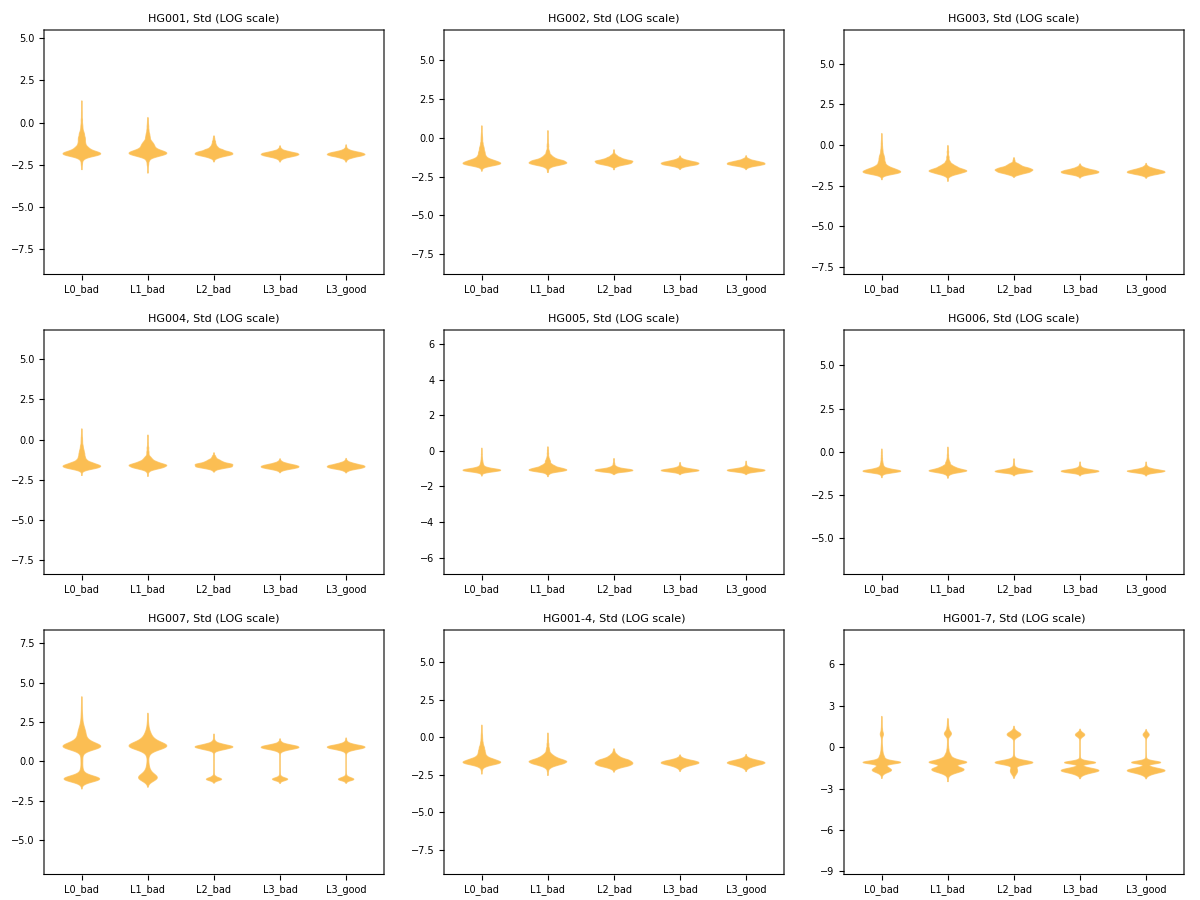
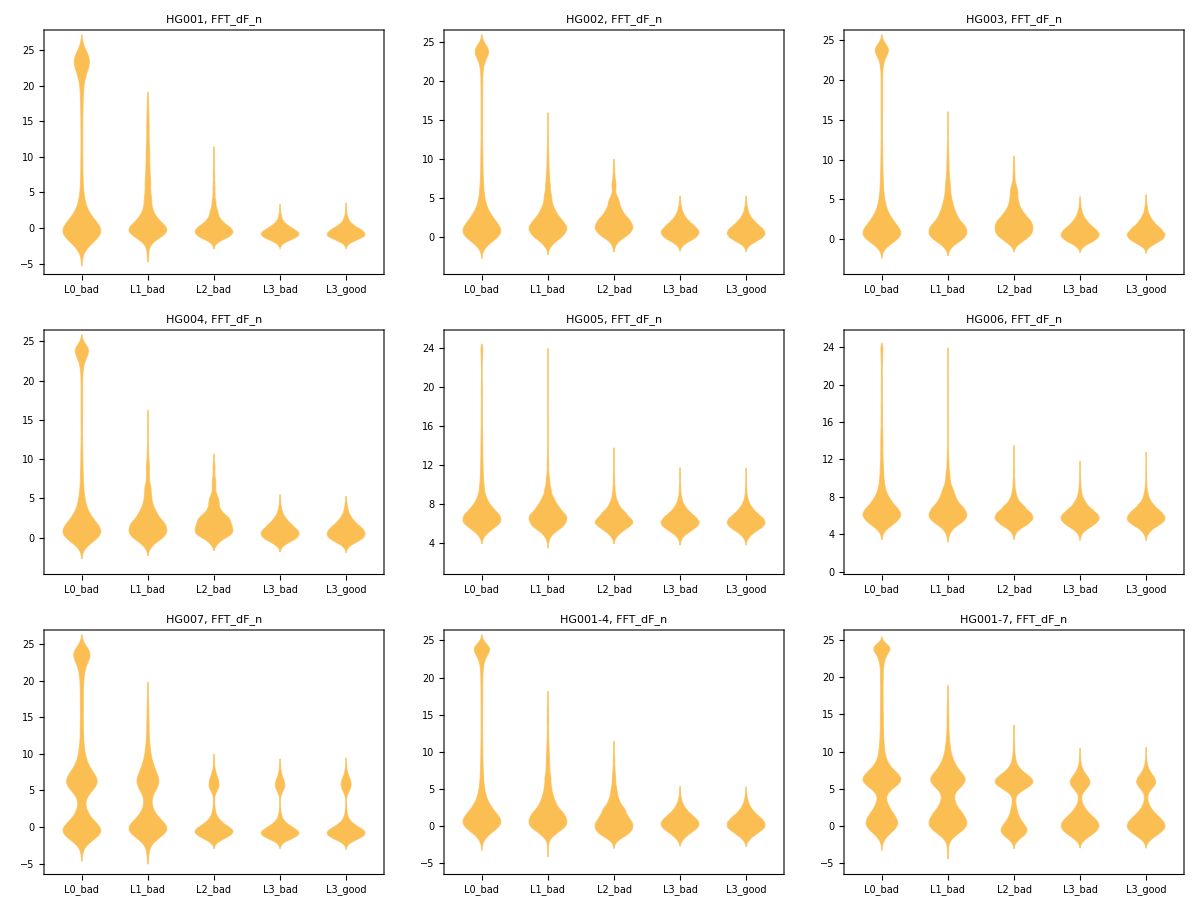
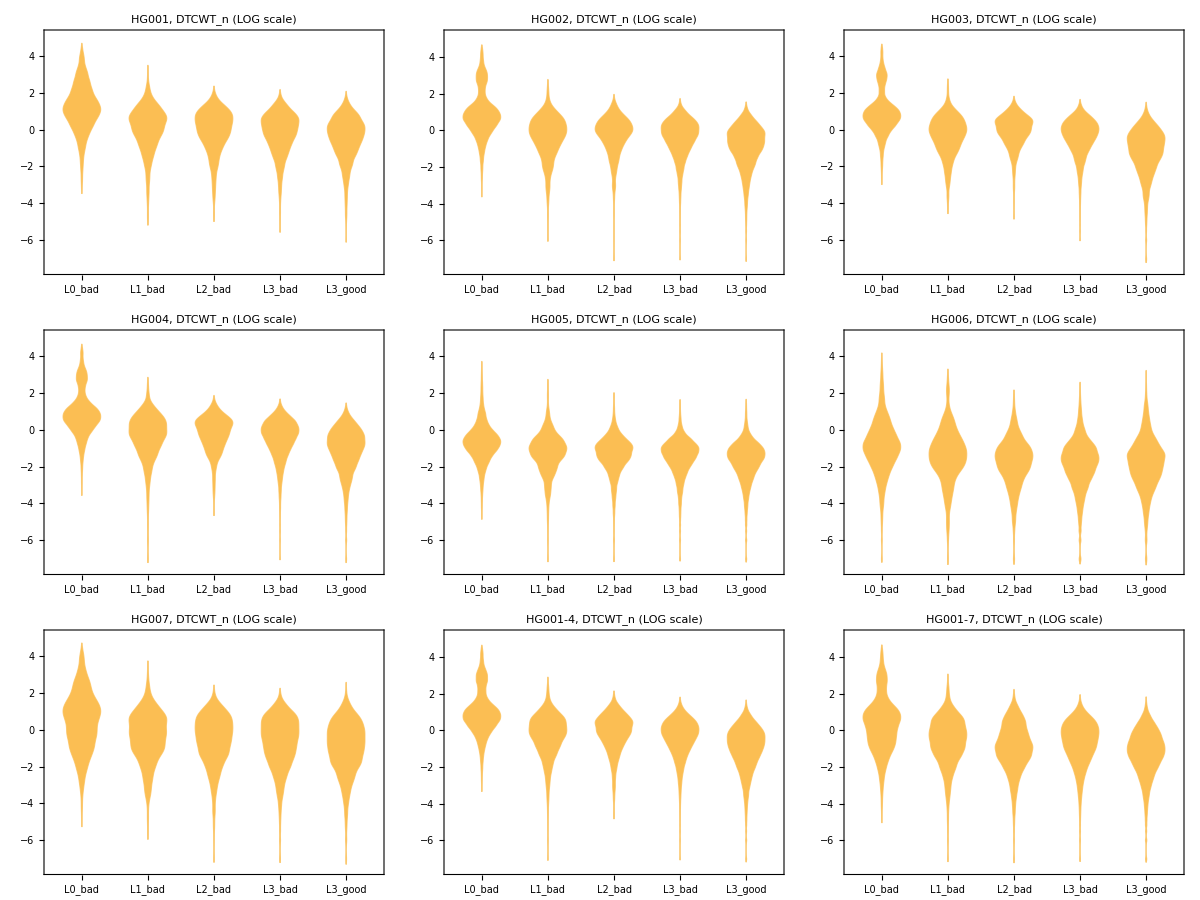
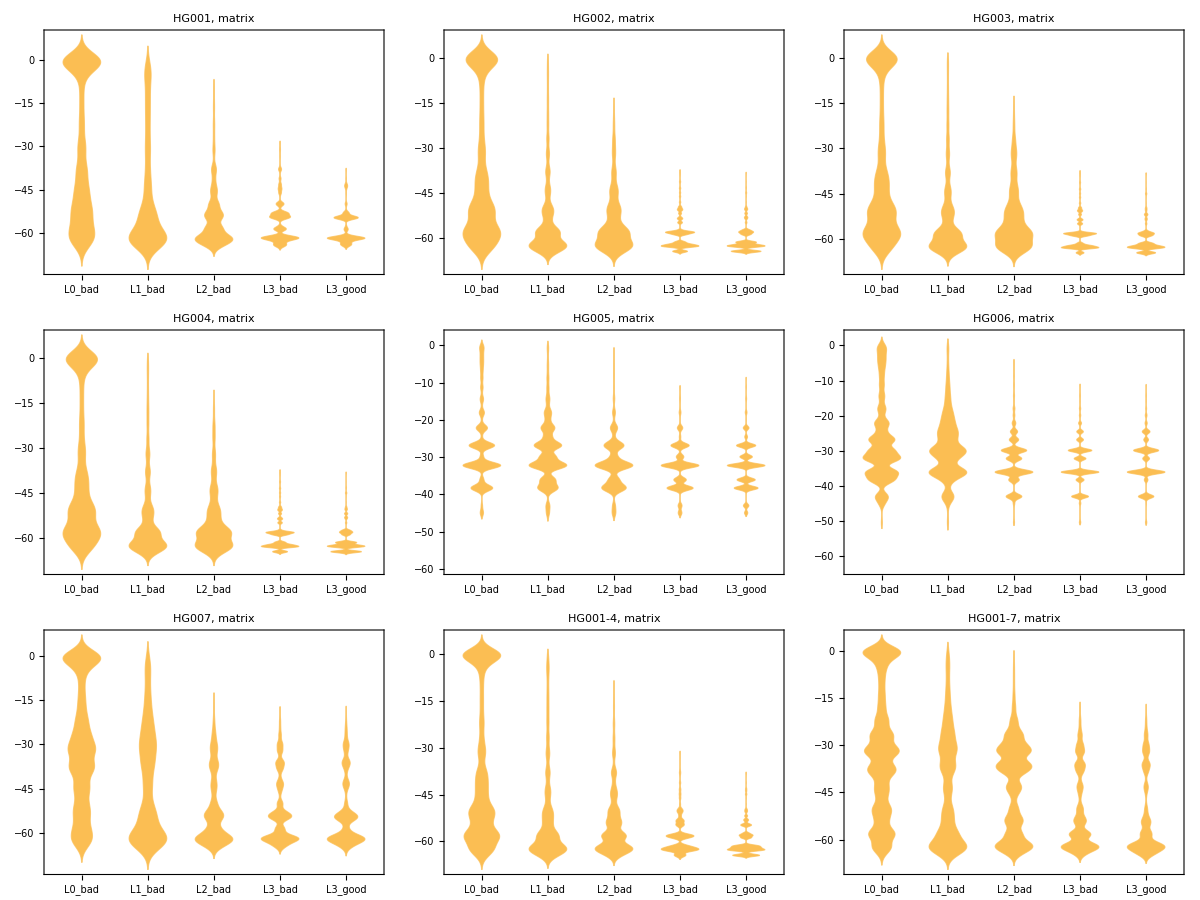
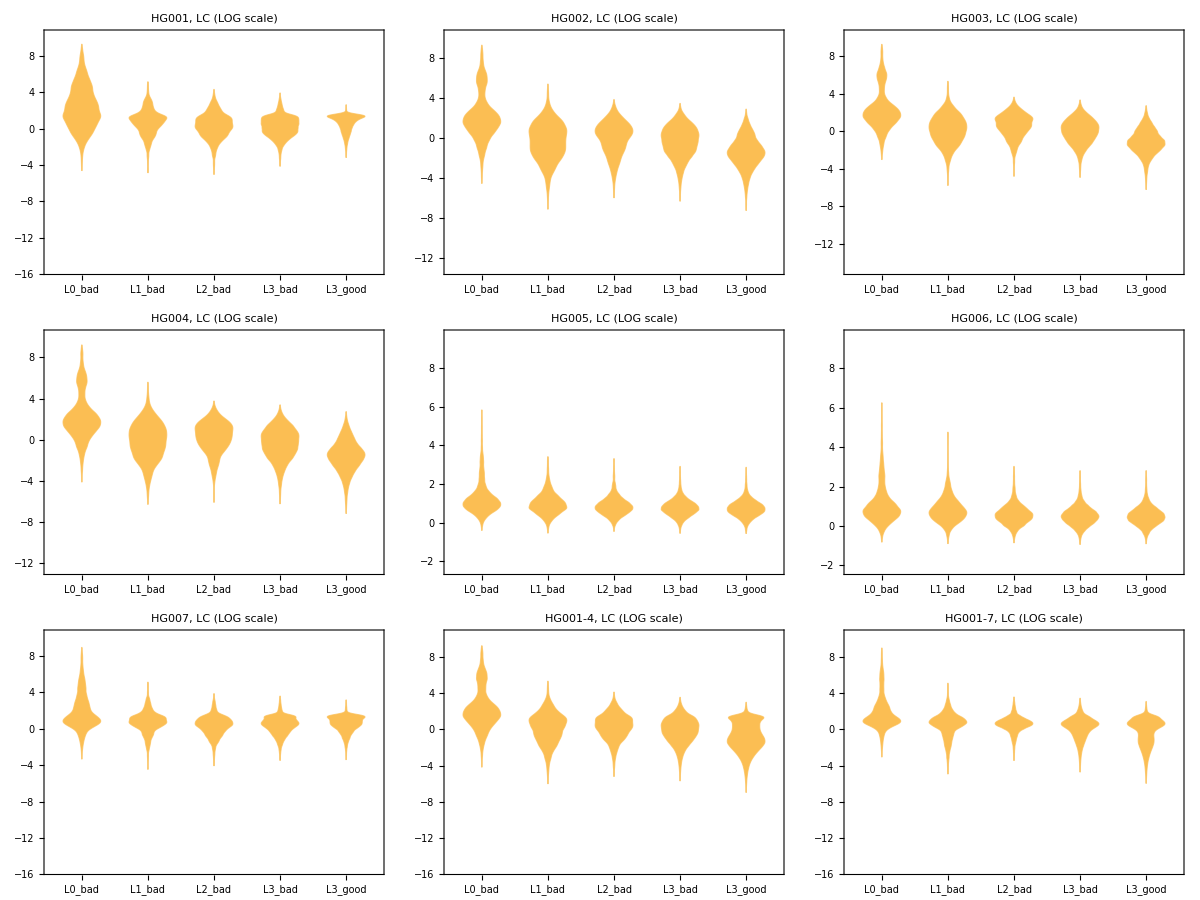

```mathematica
CH/@{"Std","FFT_dF_n","DTCWT_n","matrix","LC"}
```